```mathematica
OTC=ArrayReshape[Reverse[{542,482,553,493,551,628,691,710,696,635,641,648,707,601,582,603,595,598,673,586,507,418,373,299,283,259,220,197,169,142,128,111,100,96,94,88,81,80,72}],{39,1}];
```

```mathematica
dates=ArrayReshape[Reverse[DateRange[DateList["01 June 2017"],DateList["01 May 1998"],{-6,"Month"}]],{39,1,6}];
```

```mathematica
a=Join[dates,OTC,2];
```

```mathematica
img=DateListPlot[a,AxesLabel->{"$ trillion","A"},DateTicksFormat->{"MonthNameShort", "-", "YearShort"},FrameTicks->{{Automatic,Automatic},{{"June 1, 2001","June 1, 2005","June 1, 2009","June 1, 2013","June 1, 2017"},None}},ImageSize->Medium,FrameLabel->{,"$ Trillion"},PlotLegends->Placed[LineLegend[{"OTC Market Size"},LegendFunction->(Framed[#,RoundingRadius->0]&),LegendMargins->0],{{0.,0.0},{-0.45,-6}}],FrameStyle->Directive[FontSize->13],PlotStyle->Thickness[0.01]]
```

-Graphics-

```mathematica
Export["C:\\Users\\Miguel\\Documents\\GitHub\\Thesis\\Images\\OTC.eps",img,"eps"];
```

```mathematica
NotebookSave[]
```

```mathematica
Max[OTC]
```

710

```mathematica
K=1;
```

```mathematica
img2=Plot[{Max[x-K,0],Max[K-x,0]},{x,0,2},PlotStyle->{{Thickness[0.01],Dashing[{0.025,0.035}]},Thickness[0.01]},PlotLegends->Placed[LineLegend[{"call","put"},LegendFunction->(Framed[#,RoundingRadius->0]&),LegendMargins->0],{{0.,0.0},{-0.7,-3.4}}],ImageSize->Medium,AxesLabel->{"S(T)","Payoff"},Ticks->{{{K,"K"}},None},AxesStyle->Directive[FontSize->13]]
```

-Graphics-

```mathematica
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Thesis_Text\\Figures\\Payoff.eps",img2,"eps"];
```

```mathematica
ClearAll["Global`*"]
```

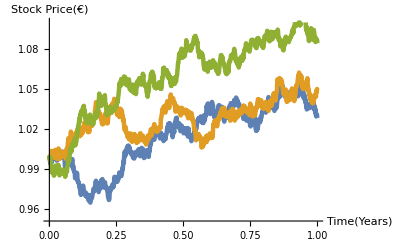

```mathematica
n=1000; (*Number of exercise points per year*)
T=1; (*Number of years in the contract*)
R=0.06;(*Yearly discount factor*)
sigma=0.05; (*Volatility of the underlying stock price*)
S0=1.; (*Initial stock price*)
dT=1/n; (*Time step duration*)
S1=Table[0,2,n*T+1]; (*Table with all the simulated paths. All entries are initially assigned 0*)
S1[[2,1]]=S0; (*Set all paths' starting points to the initial stock price*)
dW=Sqrt[dT]*RandomVariate[NormalDistribution[],{1,n*T}]; (*Matrix with the normally distributed random variables to be used in the geometric Brownian motion*)
For[i=1,i<=n*T,i++,S1[[2,i+1]]=S1[[2,i]]+R*dT*S1[[2,i]]+sigma*S1[[2,i]]*dW[[1,i]];S1[[1,i+1]]=i/n] (*Simulate geometric Brownian Motion: dS=r*S*dt+σ*S*dW *)
S2=Table[0,2,n*T+1]; (*Table with all the simulated paths. All entries are initially assigned 0*)
S2[[2,1]]=S0; (*Set all paths' starting points to the initial stock price*)
dW=Sqrt[dT]*RandomVariate[NormalDistribution[],{1,n*T}]; (*Matrix with the normally distributed random variables to be used in the geometric Brownian motion*)
For[i=1,i<=n*T,i++,S2[[2,i+1]]=S2[[2,i]]+R*dT*S2[[2,i]]+sigma*S2[[2,i]]*dW[[1,i]];S2[[1,i+1]]=i/n] (*Simulate geometric Brownian Motion: dS=r*S*dt+σ*S*dW *)
S3=Table[0,2,n*T+1]; (*Table with all the simulated paths. All entries are initially assigned 0*)
S3[[2,1]]=S0; (*Set all paths' starting points to the initial stock price*)
dW=Sqrt[dT]*RandomVariate[NormalDistribution[],{1,n*T}]; (*Matrix with the normally distributed random variables to be used in the geometric Brownian motion*)
For[i=1,i<=n*T,i++,S3[[2,i+1]]=S3[[2,i]]+R*dT*S3[[2,i]]+sigma*S3[[2,i]]*dW[[1,i]];S3[[1,i+1]]=i/n] (*Simulate geometric Brownian Motion: dS=r*S*dt+σ*S*dW *)
img3=ListPlot[{Transpose[S1],Transpose[S2],Transpose[S3]},AxesLabel->{"Time(Years)","Stock Price(€)"},Joined->True,AxesStyle->Directive[FontSize->13],PlotStyle->{Thickness[0.008]}]
```

```mathematica
(*If[True,
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Images\\GBM.eps",img3,"eps"],];*)
```

```mathematica
If[True,
Export["C:\\Users\\Miguel\\Documents\\GitHub\\Thesis\\Images\\GBM.eps",img3,"eps"],];
```

```mathematica
n=1000; (*Number of exercise points per year*)
T=1; (*Number of years in the contract*)
R=0.06;(*Yearly discount factor*)
S0=1.; (*Initial stock price*)
dT=1/n; (*Time step duration*)
dW=Sqrt[dT]*RandomVariate[NormalDistribution[],{1,n*T}]; (*Matrix with the normally distributed random variables to be used in the geometric Brownian motion*)
```

```mathematica
R=0.06;(*Yearly discount factor*)
sigma=0.05; (*Volatility of the underlying stock price*)
S1=Table[0,2,n*T+1]; (*Table with all the simulated paths. All entries are initially assigned 0*)
S1[[2,1]]=S0; (*Set all paths' starting points to the initial stock price*)
For[i=1,i<=n*T,i++,S1[[2,i+1]]=S1[[2,i]]+R*dT*S1[[2,i]]+sigma*S1[[2,i]]*dW[[1,i]];S1[[1,i+1]]=i/n] (*Simulate geometric Brownian Motion: dS=r*S*dt+σ*S*dW *)

sigma=0.055; (*Volatility of the underlying stock price*)
S2=Table[0,2,n*T+1]; (*Table with all the simulated paths. All entries are initially assigned 0*)
S2[[2,1]]=S0; (*Set all paths' starting points to the initial stock price*)
For[i=1,i<=n*T,i++,S2[[2,i+1]]=S2[[2,i]]+R*dT*S2[[2,i]]+sigma*S2[[2,i]]*dW[[1,i]];S2[[1,i+1]]=i/n] (*Simulate geometric Brownian Motion: dS=r*S*dt+σ*S*dW *)

sigma=0.06; (*Volatility of the underlying stock price*)
S3=Table[0,2,n*T+1]; (*Table with all the simulated paths. All entries are initially assigned 0*)
S3[[2,1]]=S0; (*Set all paths' starting points to the initial stock price*)
For[i=1,i<=n*T,i++,S3[[2,i+1]]=S3[[2,i]]+R*dT*S3[[2,i]]+sigma*S3[[2,i]]*dW[[1,i]];S3[[1,i+1]]=i/n] (*Simulate geometric Brownian Motion: dS=r*S*dt+σ*S*dW *)

sigma=0.065; (*Volatility of the underlying stock price*)
S4=Table[0,2,n*T+1]; (*Table with all the simulated paths. All entries are initially assigned 0*)
S4[[2,1]]=S0; (*Set all paths' starting points to the initial stock price*)
For[i=1,i<=n*T,i++,S4[[2,i+1]]=S4[[2,i]]+R*dT*S4[[2,i]]+sigma*S4[[2,i]]*dW[[1,i]];S4[[1,i+1]]=i/n] (*Simulate geometric Brownian Motion: dS=r*S*dt+σ*S*dW *)

sigma=0.07; (*Volatility of the underlying stock price*)
S5=Table[0,2,n*T+1]; (*Table with all the simulated paths. All entries are initially assigned 0*)
S5[[2,1]]=S0; (*Set all paths' starting points to the initial stock price*)
For[i=1,i<=n*T,i++,S5[[2,i+1]]=S5[[2,i]]+R*dT*S5[[2,i]]+sigma*S5[[2,i]]*dW[[1,i]];S5[[1,i+1]]=i/n] (*Simulate geometric Brownian Motion: dS=r*S*dt+σ*S*dW *)

sigma=0.075; (*Volatility of the underlying stock price*)
S6=Table[0,2,n*T+1]; (*Table with all the simulated paths. All entries are initially assigned 0*)
S6[[2,1]]=S0; (*Set all paths' starting points to the initial stock price*)
For[i=1,i<=n*T,i++,S6[[2,i+1]]=S6[[2,i]]+R*dT*S6[[2,i]]+sigma*S6[[2,i]]*dW[[1,i]];S6[[1,i+1]]=i/n] (*Simulate geometric Brownian Motion: dS=r*S*dt+σ*S*dW *)
```

```mathematica
img4={ListPlot[Transpose[S1],AxesLabel->{"Time(Years)","Stock Price(€)"},Joined->True,AxesStyle->Directive[FontSize->13],PlotStyle->{Thickness[0.004]},PlotRange->{0.96,1.09},ImageSize->Large],
ListPlot[Transpose[S2],AxesLabel->{"Time(Years)","Stock Price(€)"},Joined->True,AxesStyle->Directive[FontSize->13],PlotStyle->{Thickness[0.004]},PlotRange->{0.96,1.09},ImageSize->Large],
ListPlot[Transpose[S3],AxesLabel->{"Time(Years)","Stock Price(€)"},Joined->True,AxesStyle->Directive[FontSize->13],PlotStyle->{Thickness[0.004]},PlotRange->{0.96,1.09},ImageSize->Large],
ListPlot[Transpose[S4],AxesLabel->{"Time(Years)","Stock Price(€)"},Joined->True,AxesStyle->Directive[FontSize->13],PlotStyle->{Thickness[0.004]},PlotRange->{0.96,1.09},ImageSize->Large],
ListPlot[Transpose[S5],AxesLabel->{"Time(Years)","Stock Price(€)"},Joined->True,AxesStyle->Directive[FontSize->13],PlotStyle->{Thickness[0.004]},PlotRange->{0.96,1.09},ImageSize->Large],
ListPlot[Transpose[S6],AxesLabel->{"Time(Years)","Stock Price(€)"},Joined->True,AxesStyle->Directive[FontSize->13],PlotStyle->{Thickness[0.004]},PlotRange->{0.96,1.09},ImageSize->Large],
ListPlot[Transpose[S5],AxesLabel->{"Time(Years)","Stock Price(€)"},Joined->True,AxesStyle->Directive[FontSize->13],PlotStyle->{Thickness[0.004]},PlotRange->{0.96,1.09},ImageSize->Large],
ListPlot[Transpose[S4],AxesLabel->{"Time(Years)","Stock Price(€)"},Joined->True,AxesStyle->Directive[FontSize->13],PlotStyle->{Thickness[0.004]},PlotRange->{0.96,1.09},ImageSize->Large],
ListPlot[Transpose[S3],AxesLabel->{"Time(Years)","Stock Price(€)"},Joined->True,AxesStyle->Directive[FontSize->13],PlotStyle->{Thickness[0.004]},PlotRange->{0.96,1.09},ImageSize->Large],
ListPlot[Transpose[S2],AxesLabel->{"Time(Years)","Stock Price(€)"},Joined->True,AxesStyle->Directive[FontSize->13],PlotStyle->{Thickness[0.004]},PlotRange->{0.96,1.09},ImageSize->Large]
};
```

```mathematica
(*If[True,
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Images\\GBM.eps",img3,"eps"],];*)
```

```mathematica
If[True,
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Images\\gif_vol.gif",img4,"gif","DisplayDurations"->0.15,"Interlaced"->True,"AnimationRepetitions"->3],];
```

```mathematica
sigma=0.05; (*Volatility of the underlying stock price*)
R=0.06;(*Yearly discount factor*)
S1=Table[0,2,n*T+1]; (*Table with all the simulated paths. All entries are initially assigned 0*)
S1[[2,1]]=S0; (*Set all paths' starting points to the initial stock price*)
For[i=1,i<=n*T,i++,S1[[2,i+1]]=S1[[2,i]]+R*dT*S1[[2,i]]+sigma*S1[[2,i]]*dW[[1,i]];S1[[1,i+1]]=i/n] (*Simulate geometric Brownian Motion: dS=r*S*dt+σ*S*dW *)

R=0.065;(*Yearly discount factor*)
S2=Table[0,2,n*T+1]; (*Table with all the simulated paths. All entries are initially assigned 0*)
S2[[2,1]]=S0; (*Set all paths' starting points to the initial stock price*)
For[i=1,i<=n*T,i++,S2[[2,i+1]]=S2[[2,i]]+R*dT*S2[[2,i]]+sigma*S2[[2,i]]*dW[[1,i]];S2[[1,i+1]]=i/n] (*Simulate geometric Brownian Motion: dS=r*S*dt+σ*S*dW *)

R=0.07;(*Yearly discount factor*)
S3=Table[0,2,n*T+1]; (*Table with all the simulated paths. All entries are initially assigned 0*)
S3[[2,1]]=S0; (*Set all paths' starting points to the initial stock price*)
For[i=1,i<=n*T,i++,S3[[2,i+1]]=S3[[2,i]]+R*dT*S3[[2,i]]+sigma*S3[[2,i]]*dW[[1,i]];S3[[1,i+1]]=i/n] (*Simulate geometric Brownian Motion: dS=r*S*dt+σ*S*dW *)

R=0.075;(*Yearly discount factor*)
S4=Table[0,2,n*T+1]; (*Table with all the simulated paths. All entries are initially assigned 0*)
S4[[2,1]]=S0; (*Set all paths' starting points to the initial stock price*)
For[i=1,i<=n*T,i++,S4[[2,i+1]]=S4[[2,i]]+R*dT*S4[[2,i]]+sigma*S4[[2,i]]*dW[[1,i]];S4[[1,i+1]]=i/n] (*Simulate geometric Brownian Motion: dS=r*S*dt+σ*S*dW *)

R=0.08;(*Yearly discount factor*)
S5=Table[0,2,n*T+1]; (*Table with all the simulated paths. All entries are initially assigned 0*)
S5[[2,1]]=S0; (*Set all paths' starting points to the initial stock price*)
For[i=1,i<=n*T,i++,S5[[2,i+1]]=S5[[2,i]]+R*dT*S5[[2,i]]+sigma*S5[[2,i]]*dW[[1,i]];S5[[1,i+1]]=i/n] (*Simulate geometric Brownian Motion: dS=r*S*dt+σ*S*dW *)

R=0.085;(*Yearly discount factor*)
S6=Table[0,2,n*T+1]; (*Table with all the simulated paths. All entries are initially assigned 0*)
S6[[2,1]]=S0; (*Set all paths' starting points to the initial stock price*)
For[i=1,i<=n*T,i++,S6[[2,i+1]]=S6[[2,i]]+R*dT*S6[[2,i]]+sigma*S6[[2,i]]*dW[[1,i]];S6[[1,i+1]]=i/n] (*Simulate geometric Brownian Motion: dS=r*S*dt+σ*S*dW *)
```

```mathematica
img5={ListPlot[Transpose[S1],AxesLabel->{"Time(Years)","Stock Price(€)"},Joined->True,AxesStyle->Directive[FontSize->13],PlotStyle->{Thickness[0.004]},PlotRange->{0.96,1.09},ImageSize->Large],
ListPlot[Transpose[S2],AxesLabel->{"Time(Years)","Stock Price(€)"},Joined->True,AxesStyle->Directive[FontSize->13],PlotStyle->{Thickness[0.004]},PlotRange->{0.96,1.09},ImageSize->Large],
ListPlot[Transpose[S3],AxesLabel->{"Time(Years)","Stock Price(€)"},Joined->True,AxesStyle->Directive[FontSize->13],PlotStyle->{Thickness[0.004]},PlotRange->{0.96,1.09},ImageSize->Large],
ListPlot[Transpose[S4],AxesLabel->{"Time(Years)","Stock Price(€)"},Joined->True,AxesStyle->Directive[FontSize->13],PlotStyle->{Thickness[0.004]},PlotRange->{0.96,1.09},ImageSize->Large],
ListPlot[Transpose[S5],AxesLabel->{"Time(Years)","Stock Price(€)"},Joined->True,AxesStyle->Directive[FontSize->13],PlotStyle->{Thickness[0.004]},PlotRange->{0.96,1.09},ImageSize->Large],
ListPlot[Transpose[S6],AxesLabel->{"Time(Years)","Stock Price(€)"},Joined->True,AxesStyle->Directive[FontSize->13],PlotStyle->{Thickness[0.004]},PlotRange->{0.96,1.09},ImageSize->Large],
ListPlot[Transpose[S5],AxesLabel->{"Time(Years)","Stock Price(€)"},Joined->True,AxesStyle->Directive[FontSize->13],PlotStyle->{Thickness[0.004]},PlotRange->{0.96,1.09},ImageSize->Large],
ListPlot[Transpose[S4],AxesLabel->{"Time(Years)","Stock Price(€)"},Joined->True,AxesStyle->Directive[FontSize->13],PlotStyle->{Thickness[0.004]},PlotRange->{0.96,1.09},ImageSize->Large],
ListPlot[Transpose[S3],AxesLabel->{"Time(Years)","Stock Price(€)"},Joined->True,AxesStyle->Directive[FontSize->13],PlotStyle->{Thickness[0.004]},PlotRange->{0.96,1.09},ImageSize->Large],
ListPlot[Transpose[S2],AxesLabel->{"Time(Years)","Stock Price(€)"},Joined->True,AxesStyle->Directive[FontSize->13],PlotStyle->{Thickness[0.004]},PlotRange->{0.96,1.09},ImageSize->Large],
ListPlot[Transpose[S1],AxesLabel->{"Time(Years)","Stock Price(€)"},Joined->True,AxesStyle->Directive[FontSize->13],PlotStyle->{Thickness[0.004]},PlotRange->{0.96,1.09},ImageSize->Large]
};
```

```mathematica
If[True,
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Images\\gif_int.gif",img5,"gif","DisplayDurations"->0.15,"Interlaced"->True],];
```

```mathematica
img7=ListPlot[Transpose[S1],AxesLabel->{"Time(Years)","Stock Price(€)"},Joined->True,AxesStyle->Directive[FontSize->13],PlotStyle->{Thickness[0.004]},PlotRange->{0.96,1.09},ImageSize->Large];
```

```mathematica
If[True,
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Images\\gif_0.gif",img7,"gif","DisplayDurations"->0.15,"Interlaced"->True],];
```

```mathematica
R=0.06;(*Yearly discount factor*)
sigma=0.05; (*Volatility of the underlying stock price*)

S1=Table[0,2,n*T+1]; (*Table with all the simulated paths. All entries are initially assigned 0*)
S1[[2,1]]=S0; (*Set all paths' starting points to the initial stock price*)
For[i=1,i<=n*T,i++,S1[[2,i+1]]=S1[[2,i]]+R*dT*S1[[2,i]]+sigma*S1[[2,i]]*dW[[1,i]];S1[[1,i+1]]=i/n] (*Simulate geometric Brownian Motion: dS=r*S*dt+σ*S*dW2 *)

dW2=Sqrt[dT]*RandomVariate[NormalDistribution[],{1,n*T}]; 
S2=Table[0,2,n*T+1]; (*Table with all the simulated paths. All entries are initially assigned 0*)
S2[[2,1]]=S0; (*Set all paths' starting points to the initial stock price*)
For[i=1,i<=n*T,i++,S2[[2,i+1]]=S2[[2,i]]+R*dT*S2[[2,i]]+sigma*S2[[2,i]]*dW2[[1,i]];S2[[1,i+1]]=i/n] (*Simulate geometric Brownian Motion: dS=r*S*dt+σ*S*dW2 *)

dW2=Sqrt[dT]*RandomVariate[NormalDistribution[],{1,n*T}]; 
S3=Table[0,2,n*T+1]; (*Table with all the simulated paths. All entries are initially assigned 0*)
S3[[2,1]]=S0; (*Set all paths' starting points to the initial stock price*)
For[i=1,i<=n*T,i++,S3[[2,i+1]]=S3[[2,i]]+R*dT*S3[[2,i]]+sigma*S3[[2,i]]*dW2[[1,i]];S3[[1,i+1]]=i/n] (*Simulate geometric Brownian Motion: dS=r*S*dt+σ*S*dW2 *)

dW2=Sqrt[dT]*RandomVariate[NormalDistribution[],{1,n*T}]; 
S4=Table[0,2,n*T+1]; (*Table with all the simulated paths. All entries are initially assigned 0*)
S4[[2,1]]=S0; (*Set all paths' starting points to the initial stock price*)
For[i=1,i<=n*T,i++,S4[[2,i+1]]=S4[[2,i]]+R*dT*S4[[2,i]]+sigma*S4[[2,i]]*dW2[[1,i]];S4[[1,i+1]]=i/n] (*Simulate geometric Brownian Motion: dS=r*S*dt+σ*S*dW2 *)

dW2=Sqrt[dT]*RandomVariate[NormalDistribution[],{1,n*T}]; 
S5=Table[0,2,n*T+1]; (*Table with all the simulated paths. All entries are initially assigned 0*)
S5[[2,1]]=S0; (*Set all paths' starting points to the initial stock price*)
For[i=1,i<=n*T,i++,S5[[2,i+1]]=S5[[2,i]]+R*dT*S5[[2,i]]+sigma*S5[[2,i]]*dW2[[1,i]];S5[[1,i+1]]=i/n] (*Simulate geometric Brownian Motion: dS=r*S*dt+σ*S*dW2 *)

dW2=Sqrt[dT]*RandomVariate[NormalDistribution[],{1,n*T}]; 
S6=Table[0,2,n*T+1]; (*Table with all the simulated paths. All entries are initially assigned 0*)
S6[[2,1]]=S0; (*Set all paths' starting points to the initial stock price*)
For[i=1,i<=n*T,i++,S6[[2,i+1]]=S6[[2,i]]+R*dT*S6[[2,i]]+sigma*S6[[2,i]]*dW2[[1,i]];S6[[1,i+1]]=i/n] (*Simulate geometric Brownian Motion: dS=r*S*dt+σ*S*dW2 *)
```

```mathematica
img6={ListPlot[Transpose[S1],AxesLabel->{"Time(Years)","Stock Price(€)"},Joined->True,AxesStyle->Directive[FontSize->13],PlotStyle->{Thickness[0.004]},PlotRange->{0.96,1.09},ImageSize->Large],
ListPlot[Transpose[S2],AxesLabel->{"Time(Years)","Stock Price(€)"},Joined->True,AxesStyle->Directive[FontSize->13],PlotStyle->{Thickness[0.004]},PlotRange->{0.96,1.09},ImageSize->Large],
ListPlot[Transpose[S3],AxesLabel->{"Time(Years)","Stock Price(€)"},Joined->True,AxesStyle->Directive[FontSize->13],PlotStyle->{Thickness[0.004]},PlotRange->{0.96,1.09},ImageSize->Large],
ListPlot[Transpose[S1],AxesLabel->{"Time(Years)","Stock Price(€)"},Joined->True,AxesStyle->Directive[FontSize->13],PlotStyle->{Thickness[0.004]},PlotRange->{0.96,1.09},ImageSize->Large]
};
```

```mathematica
If[True,
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Images\\gif_N.gif",img6,"gif","DisplayDurations"->.7],];
```

```mathematica
img6={ListPlot[Transpose[S1],AxesLabel->{"Time(Years)","Stock Price(€)"},Joined->True,AxesStyle->Directive[FontSize->13],PlotStyle->{Thickness[0.004]},PlotRange->{0.96,1.09},ImageSize->Large],
ListPlot[Transpose[S2],AxesLabel->{"Time(Years)","Stock Price(€)"},Joined->True,AxesStyle->Directive[FontSize->13],PlotStyle->{Thickness[0.004]},PlotRange->{0.96,1.09},ImageSize->Large],
ListPlot[Transpose[S3],AxesLabel->{"Time(Years)","Stock Price(€)"},Joined->True,AxesStyle->Directive[FontSize->13],PlotStyle->{Thickness[0.004]},PlotRange->{0.96,1.09},ImageSize->Large],
ListPlot[Transpose[S4],AxesLabel->{"Time(Years)","Stock Price(€)"},Joined->True,AxesStyle->Directive[FontSize->13],PlotStyle->{Thickness[0.004]},PlotRange->{0.96,1.09},ImageSize->Large],
ListPlot[Transpose[S5],AxesLabel->{"Time(Years)","Stock Price(€)"},Joined->True,AxesStyle->Directive[FontSize->13],PlotStyle->{Thickness[0.004]},PlotRange->{0.96,1.09},ImageSize->Large],
ListPlot[Transpose[S6],AxesLabel->{"Time(Years)","Stock Price(€)"},Joined->True,AxesStyle->Directive[FontSize->13],PlotStyle->{Thickness[0.004]},PlotRange->{0.96,1.09},ImageSize->Large]
};
```

```mathematica
n=1000; (*Number of exercise points per year*)
T=1; (*Number of years in the contract*)
R=0.06;(*Yearly discount factor*)
sigma=0.05; (*Volatility of the underlying stock price*)
S0=1.; (*Initial stock price*)
dT=1/n; (*Time step duration*)

S1=Table[0,2,n*T+1]; (*Table with all the simulated paths. All entries are initially assigned 0*)
S1[[2,1]]=S0; (*Set all paths' starting points to the initial stock price*)
For[i=1,i<=n*T,i++,S1[[2,i+1]]=S1[[2,i]]+R*dT*S1[[2,i]]+sigma*S1[[2,i]]*dW[[1,i]];S1[[1,i+1]]=i/n] (*Simulate geometric Brownian Motion: dS=r*S*dt+σ*S*dW3 *)

S2=Table[0,2,n*T+1]; (*Table with all the simulated paths. All entries are initially assigned 0*)
S2[[2,1]]=S0; (*Set all paths' starting points to the initial stock price*)
dW3=Sqrt[dT]*RandomVariate[NormalDistribution[],{1,n*T}]; (*Matrix with the normally distributed random variables to be used in the geometric Brownian motion*)
For[i=1,i<=n*T,i++,S2[[2,i+1]]=S2[[2,i]]+R*dT*S2[[2,i]]+sigma*S2[[2,i]]*dW3[[1,i]];S2[[1,i+1]]=i/n] (*Simulate geometric Brownian Motion: dS=r*S*dt+σ*S*dW3 *)
S3=Table[0,2,n*T+1]; (*Table with all the simulated paths. All entries are initially assigned 0*)
S3[[2,1]]=S0; (*Set all paths' starting points to the initial stock price*)
dW3=Sqrt[dT]*RandomVariate[NormalDistribution[],{1,n*T}]; (*Matrix with the normally distributed random variables to be used in the geometric Brownian motion*)
For[i=1,i<=n*T,i++,S3[[2,i+1]]=S3[[2,i]]+R*dT*S3[[2,i]]+sigma*S3[[2,i]]*dW3[[1,i]];S3[[1,i+1]]=i/n] (*Simulate geometric Brownian Motion: dS=r*S*dt+σ*S*dW3 *)
S4=Table[0,2,n*T+1]; (*Table with all the simulated paths. All entries are initially assigned 0*)
S4[[2,1]]=S0; (*Set all paths' starting points to the initial stock price*)
dW3=Sqrt[dT]*RandomVariate[NormalDistribution[],{1,n*T}]; (*Matrix with the normally distributed random variables to be used in the geometric Brownian motion*)
For[i=1,i<=n*T,i++,S4[[2,i+1]]=S4[[2,i]]+R*dT*S4[[2,i]]+sigma*S4[[2,i]]*dW3[[1,i]];S4[[1,i+1]]=i/n] (*Simulate geometric Brownian Motion: dS=r*S*dt+σ*S*dW3 *)
S5=Table[0,2,n*T+1]; (*Table with all the simulated paths. All entries are initially assigned 0*)
S5[[2,1]]=S0; (*Set all paths' starting points to the initial stock price*)
dW3=Sqrt[dT]*RandomVariate[NormalDistribution[],{1,n*T}]; (*Matrix with the normally distributed random variables to be used in the geometric Brownian motion*)
For[i=1,i<=n*T,i++,S5[[2,i+1]]=S5[[2,i]]+R*dT*S5[[2,i]]+sigma*S5[[2,i]]*dW3[[1,i]];S5[[1,i+1]]=i/n] (*Simulate geometric Brownian Motion: dS=r*S*dt+σ*S*dW3 *)
S6=Table[0,2,n*T+1]; (*Table with all the simulated paths. All entries are initially assigned 0*)
S6[[2,1]]=S0; (*Set all paths' starting points to the initial stock price*)
dW3=Sqrt[dT]*RandomVariate[NormalDistribution[],{1,n*T}]; (*Matrix with the normally distributed random variables to be used in the geometric Brownian motion*)
For[i=1,i<=n*T,i++,S6[[2,i+1]]=S6[[2,i]]+R*dT*S6[[2,i]]+sigma*S6[[2,i]]*dW3[[1,i]];S6[[1,i+1]]=i/n] (*Simulate geometric Brownian Motion: dS=r*S*dt+σ*S*dW3 *)
S7=Table[0,2,n*T+1]; (*Table with all the simulated paths. All entries are initially assigned 0*)
S7[[2,1]]=S0; (*Set all paths' starting points to the initial stock price*)
dW3=Sqrt[dT]*RandomVariate[NormalDistribution[],{1,n*T}]; (*Matrix with the normally distributed random variables to be used in the geometric Brownian motion*)
For[i=1,i<=n*T,i++,S7[[2,i+1]]=S7[[2,i]]+R*dT*S7[[2,i]]+sigma*S7[[2,i]]*dW3[[1,i]];S7[[1,i+1]]=i/n] (*Simulate geometric Brownian Motion: dS=r*S*dt+σ*S*dW3 *)
S8=Table[0,2,n*T+1]; (*Table with all the simulated paths. All entries are initially assigned 0*)
S8[[2,1]]=S0; (*Set all paths' starting points to the initial stock price*)
dW3=Sqrt[dT]*RandomVariate[NormalDistribution[],{1,n*T}]; (*Matrix with the normally distributed random variables to be used in the geometric Brownian motion*)
For[i=1,i<=n*T,i++,S8[[2,i+1]]=S8[[2,i]]+R*dT*S8[[2,i]]+sigma*S8[[2,i]]*dW3[[1,i]];S8[[1,i+1]]=i/n] (*Simulate geometric Brownian Motion: dS=r*S*dt+σ*S*dW3 *)
S9=Table[0,2,n*T+1]; (*Table with all the simulated paths. All entries are initially assigned 0*)
S9[[2,1]]=S0; (*Set all paths' starting points to the initial stock price*)
dW3=Sqrt[dT]*RandomVariate[NormalDistribution[],{1,n*T}]; (*Matrix with the normally distributed random variables to be used in the geometric Brownian motion*)
For[i=1,i<=n*T,i++,S9[[2,i+1]]=S9[[2,i]]+R*dT*S9[[2,i]]+sigma*S9[[2,i]]*dW3[[1,i]];S9[[1,i+1]]=i/n] (*Simulate geometric Brownian Motion: dS=r*S*dt+σ*S*dW3 *)
S10=Table[0,2,n*T+1]; (*Table with all the simulated paths. All entries are initially assigned 0*)
S10[[2,1]]=S0; (*Set all paths' starting points to the initial stock price*)
dW3=Sqrt[dT]*RandomVariate[NormalDistribution[],{1,n*T}]; (*Matrix with the normally distributed random variables to be used in the geometric Brownian motion*)
For[i=1,i<=n*T,i++,S10[[2,i+1]]=S10[[2,i]]+R*dT*S10[[2,i]]+sigma*S10[[2,i]]*dW3[[1,i]];S10[[1,i+1]]=i/n] (*Simulate geometric Brownian Motion: dS=r*S*dt+σ*S*dW3 *)
S11=Table[0,2,n*T+1]; (*Table with all the simulated paths. All entries are initially assigned 0*)
S11[[2,1]]=S0; (*Set all paths' starting points to the initial stock price*)
dW3=Sqrt[dT]*RandomVariate[NormalDistribution[],{1,n*T}]; (*Matrix with the normally distributed random variables to be used in the geometric Brownian motion*)
For[i=1,i<=n*T,i++,S11[[2,i+1]]=S11[[2,i]]+R*dT*S11[[2,i]]+sigma*S11[[2,i]]*dW3[[1,i]];S11[[1,i+1]]=i/n] (*Simulate geometric Brownian Motion: dS=r*S*dt+σ*S*dW3 *)
S12=Table[0,2,n*T+1]; (*Table with all the simulated paths. All entries are initially assigned 0*)
S12[[2,1]]=S0; (*Set all paths' starting points to the initial stock price*)
dW3=Sqrt[dT]*RandomVariate[NormalDistribution[],{1,n*T}]; (*Matrix with the normally distributed random variables to be used in the geometric Brownian motion*)
For[i=1,i<=n*T,i++,S12[[2,i+1]]=S12[[2,i]]+R*dT*S12[[2,i]]+sigma*S12[[2,i]]*dW3[[1,i]];S12[[1,i+1]]=i/n] (*Simulate geometric Brownian Motion: dS=r*S*dt+σ*S*dW3 *)
S13=Table[0,2,n*T+1]; (*Table with all the simulated paths. All entries are initially assigned 0*)
S13[[2,1]]=S0; (*Set all paths' starting points to the initial stock price*)
dW3=Sqrt[dT]*RandomVariate[NormalDistribution[],{1,n*T}]; (*Matrix with the normally distributed random variables to be used in the geometric Brownian motion*)
For[i=1,i<=n*T,i++,S13[[2,i+1]]=S13[[2,i]]+R*dT*S13[[2,i]]+sigma*S13[[2,i]]*dW3[[1,i]];S13[[1,i+1]]=i/n] (*Simulate geometric Brownian Motion: dS=r*S*dt+σ*S*dW3 *)
S14=Table[0,2,n*T+1]; (*Table with all the simulated paths. All entries are initially assigned 0*)
S14[[2,1]]=S0; (*Set all paths' starting points to the initial stock price*)
dW3=Sqrt[dT]*RandomVariate[NormalDistribution[],{1,n*T}]; (*Matrix with the normally distributed random variables to be used in the geometric Brownian motion*)
For[i=1,i<=n*T,i++,S14[[2,i+1]]=S14[[2,i]]+R*dT*S14[[2,i]]+sigma*S14[[2,i]]*dW3[[1,i]];S14[[1,i+1]]=i/n] (*Simulate geometric Brownian Motion: dS=r*S*dt+σ*S*dW3 *)
S15=Table[0,2,n*T+1]; (*Table with all the simulated paths. All entries are initially assigned 0*)
S15[[2,1]]=S0; (*Set all paths' starting points to the initial stock price*)
dW3=Sqrt[dT]*RandomVariate[NormalDistribution[],{1,n*T}]; (*Matrix with the normally distributed random variables to be used in the geometric Brownian motion*)
For[i=1,i<=n*T,i++,S15[[2,i+1]]=S15[[2,i]]+R*dT*S15[[2,i]]+sigma*S15[[2,i]]*dW3[[1,i]];S15[[1,i+1]]=i/n] (*Simulate geometric Brownian Motion: dS=r*S*dt+σ*S*dW3 *)
S16=Table[0,2,n*T+1]; (*Table with all the simulated paths. All entries are initially assigned 0*)
S16[[2,1]]=S0; (*Set all paths' starting points to the initial stock price*)
dW3=Sqrt[dT]*RandomVariate[NormalDistribution[],{1,n*T}]; (*Matrix with the normally distributed random variables to be used in the geometric Brownian motion*)
For[i=1,i<=n*T,i++,S16[[2,i+1]]=S16[[2,i]]+R*dT*S16[[2,i]]+sigma*S16[[2,i]]*dW3[[1,i]];S16[[1,i+1]]=i/n] (*Simulate geometric Brownian Motion: dS=r*S*dt+σ*S*dW3 *)
S17=Table[0,2,n*T+1]; (*Table with all the simulated paths. All entries are initially assigned 0*)
S17[[2,1]]=S0; (*Set all paths' starting points to the initial stock price*)
dW3=Sqrt[dT]*RandomVariate[NormalDistribution[],{1,n*T}]; (*Matrix with the normally distributed random variables to be used in the geometric Brownian motion*)
For[i=1,i<=n*T,i++,S17[[2,i+1]]=S17[[2,i]]+R*dT*S17[[2,i]]+sigma*S17[[2,i]]*dW3[[1,i]];S17[[1,i+1]]=i/n] (*Simulate geometric Brownian Motion: dS=r*S*dt+σ*S*dW3 *)
S18=Table[0,2,n*T+1]; (*Table with all the simulated paths. All entries are initially assigned 0*)
S18[[2,1]]=S0; (*Set all paths' starting points to the initial stock price*)
dW3=Sqrt[dT]*RandomVariate[NormalDistribution[],{1,n*T}]; (*Matrix with the normally distributed random variables to be used in the geometric Brownian motion*)
For[i=1,i<=n*T,i++,S18[[2,i+1]]=S18[[2,i]]+R*dT*S18[[2,i]]+sigma*S18[[2,i]]*dW3[[1,i]];S18[[1,i+1]]=i/n] (*Simulate geometric Brownian Motion: dS=r*S*dt+σ*S*dW3 *)
S19=Table[0,2,n*T+1]; (*Table with all the simulated paths. All entries are initially assigned 0*)
S19[[2,1]]=S0; (*Set all paths' starting points to the initial stock price*)
dW3=Sqrt[dT]*RandomVariate[NormalDistribution[],{1,n*T}]; (*Matrix with the normally distributed random variables to be used in the geometric Brownian motion*)
For[i=1,i<=n*T,i++,S19[[2,i+1]]=S19[[2,i]]+R*dT*S19[[2,i]]+sigma*S19[[2,i]]*dW3[[1,i]];S19[[1,i+1]]=i/n] (*Simulate geometric Brownian Motion: dS=r*S*dt+σ*S*dW3 *)
S20=Table[0,2,n*T+1]; (*Table with all the simulated paths. All entries are initially assigned 0*)
S20[[2,1]]=S0; (*Set all paths' starting points to the initial stock price*)
dW3=Sqrt[dT]*RandomVariate[NormalDistribution[],{1,n*T}]; (*Matrix with the normally distributed random variables to be used in the geometric Brownian motion*)
For[i=1,i<=n*T,i++,S20[[2,i+1]]=S20[[2,i]]+R*dT*S20[[2,i]]+sigma*S20[[2,i]]*dW3[[1,i]];S20[[1,i+1]]=i/n] (*Simulate geometric Brownian Motion: dS=r*S*dt+σ*S*dW3 *)
```

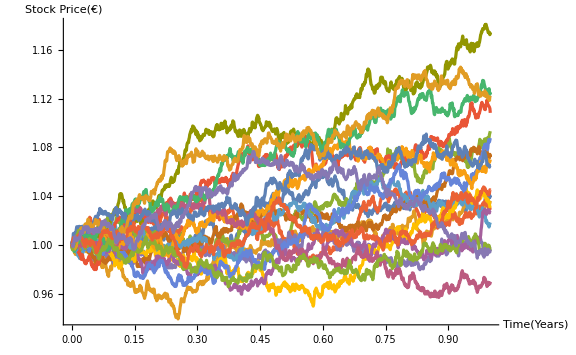

```mathematica
img8=ListPlot[{Transpose[S1],Transpose[S2],Transpose[S3],Transpose[S4],Transpose[S5],Transpose[S6],Transpose[S7],Transpose[S8],Transpose[S9],Transpose[S10],Transpose[S11],Transpose[S12],Transpose[S13],Transpose[S14],Transpose[S15],Transpose[S16],Transpose[S17],Transpose[S18],Transpose[S19],Transpose[S20]},AxesLabel->{"Time(Years)","Stock Price(€)"},Joined->True,AxesStyle->Directive[FontSize->13],PlotStyle->{Thickness[0.004]},PlotRange->Full,ImageSize->Large]
```

```mathematica
If[True,
Export["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Images\\mult.gif",img8,"gif"],];
```